```mathematica
SetDirectory["~/Cellular-Automata"];
Width=32;
Height=64;
uniqueRuleTable={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,18,19,22,23,24,25,26,27,28,29,30,32,33,34,35,36,37,38,40,41,42,43,44,45,46,50,51,54,56,57,58,60,62,72,73,74,76,77,78,90,94,104,105,106,108,110,122,126,128,130,132,134,136,138,140,142,146,150,152,154,156,160,162,164,168,170,172,178,184,200,204,232};
makePic[Width_,Height_,data_]:=Table[{If[data[[j,i]]==1,Black,White],Polygon[{{i,-j},{i+1,-j},{(data[[j+1,Width+1]]-1)(i+1)-(data[[j+1,Width+1]]-2)(Width/2+1),-j-1},{(data[[j+1,Width+1]]-1)(i)-(data[[j+1,Width+1]]-2)(Width/2+1),-j-1}}]},{i,1,Width},{j,1,5/4 Height}];
Run["./RunSim -s 271 -b -e 5"];
data=Import["./rule_num_30.csv"];
```

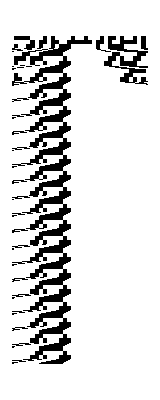

```mathematica
pic=makePic[Width,Height,data];
(*Export["rule_num_30.gif",Graphics[pic,PlotRange->{{1,17},All}]]*)
Graphics[pic,PlotRange->{{1,Width+1},All}]
```

```mathematica
Do[
data=Import["./rule_num_"<>ToString[uniqueRuleTable[[k]]]<>".csv"];
Export["rule_num_"<>ToString[uniqueRuleTable[[k]]]<>".gif",
Graphics[makePic[Width,Height,data],
PlotRange->{{1,Width+1},All}]],{k,1,88,1}]
```